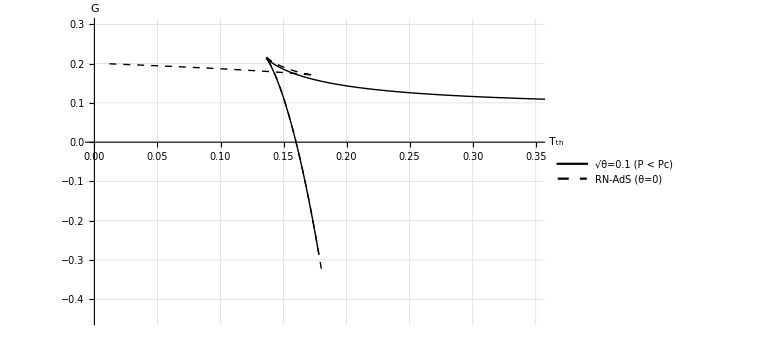

```mathematica
ClearAll["Global`*"];
Q=0.2;l=2;sth=0.01;P=3/(8 Pi l^2);

(*-----Fonctions déformées-----*)
rθ[r_,s_]:=(2 r/Pi) ArcTan[r/Sqrt[s]];
drθ[r_,s_]:=2/Pi (ArcTan[r/Sqrt[s]]+(r s)/(r^2+s^2));
μ[r_,s_]:=(2/Pi) (ArcTan[r/Sqrt[s]]-(r s)/(r^2+s^2));
Qθ[r_,s_]:=Q μ[r,s];
dQθ[r_,s_]:=(4 Q r^2 Sqrt[s])/(Pi (r^2+s)^2);

TthDef[rh_,s_]:=Module[{ρ=rθ[rh,s],Qh=Qθ[rh,s],dQ=dQθ[rh,s],dρ=drθ[rh,s]},1/(4 Pi ρ) (1-Qh^2/ρ^2+3 ρ^2/l^2)+(Qh/(2 Pi ρ^2))*(dQ/dρ)];

GibbsDef[rh_,s_]:=Module[{ρ=rθ[rh,s],T=TthDef[rh,s],Qh=Qθ[rh,s],χ=dQθ[rh,s]/drθ[rh,s]},Pi ρ^2 T-(8 Pi P ρ^3)/3+Qh^2/ρ-Qh χ];

(*-----Fonctions commutatives-----*)
TthCom[rh_]:=(1/(4 Pi rh)) (1-Q^2/rh^2+3 rh^2/l^2);
GibbsCom[rh_]:=Module[{T=TthCom[rh]},Pi rh^2 T-(8 Pi P rh^3)/3+Q^2/rh];

(*-----Points (plage restreinte)-----*)
rVals=Join[Range[0.2,0.5,0.005],Range[0.5,2.5,0.02]];
ptsDef=Select[Table[{TthDef[r,sth],GibbsDef[r,sth]},{r,rVals}],NumericQ[#[[1]]]&&NumericQ[#[[2]]]&&#[[1]]>0&];
ptsCom=Select[Table[{TthCom[r],GibbsCom[r]},{r,rVals}],NumericQ[#[[1]]]&&NumericQ[#[[2]]]&&#[[1]]>0&];

(*-----Tracé avec zoom-----*)
 figGibbs=ListLinePlot[{ptsDef,ptsCom},PlotStyle->{{Black,Thick},{Black,Dashed,Thin}},PlotLegends->Placed[LineLegend[{Directive[Black,Thick],Directive[Black,Dashed,Thin]},{"\!\(\*SqrtBox[\(θ\)]\)=0.1 (P < Pc)","RN-AdS (θ=0)"},LegendFunction->(Framed[#,Background->White,FrameStyle->Black]&)],{0.8,0.2}],AxesLabel->{Style[Subscript["T","th"],16],Style["G",16]},LabelStyle->Directive[14],PlotRange->{{0,0.35},{-0.45,0.3}},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->Large,Joined->True]
```

```mathematica
Export["gibbs_energy.eps",figGibbs,ImageResolution->1200];
```